# Promise

## User cost

```mathematica
cost[cost_, rate_, mul_, pay_] = rate * mul * pay - cost;
DensityPlot3D[costbound[c, 0.05, m, p], {c, 0.01, 1.},{m, 1, 100}, {p, 0.01, 1.0}, AxesLabel->{"cost", "multiplier", "payment"}, PlotLegends->Automatic, PlotRange->{All, All, All, {-1,0}}, OpacityFunction->None]
```

-Graphics3D-

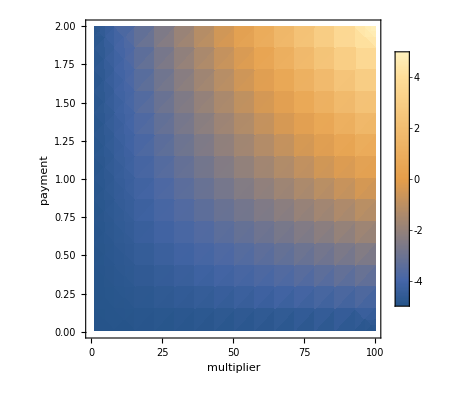

```mathematica
DensityPlot[costbound[5, 0.05, m, p],{m, 1, 100}, {p, 0.01, 2.0}, FrameLabel->{"multiplier", "payment"}, PlotLegends->Automatic, PlotRange->{-10,10}]
```

```mathematica
beta[delta_, r_, t_, m_, D_, V_] = (Sum[((delta/(1+r))^t)*(p - t* r * p - r * D),{t, 0, m}])/(Sum[((delta/(1+r))^t)*(V- r*D - D),{t, 0, m}]);
```

## Service provider cost

```mathematica
rho[delta_,r_, t_, m_, D_, p_] = (Sum[((delta/1+r)^t)*(p-(t+1)*r*p-r*D), {t,1,m-1}])/(- Sum[((delta/1+r)^t)*(r), {t,1,m-1}]);
rho2[delta_,r_, t_, m_, D_, p_] = (Sum[((delta/1+r)^t)*(p-(t+1)*r*p-r*D), {t,0,m-1}]);
mydelta = 0.75;
myr = 0.0375/365;
mym=10;
myD= 2;
myp= 0.009375;
myV=2;
linear = myp - myr*myp + myD - myV;
```

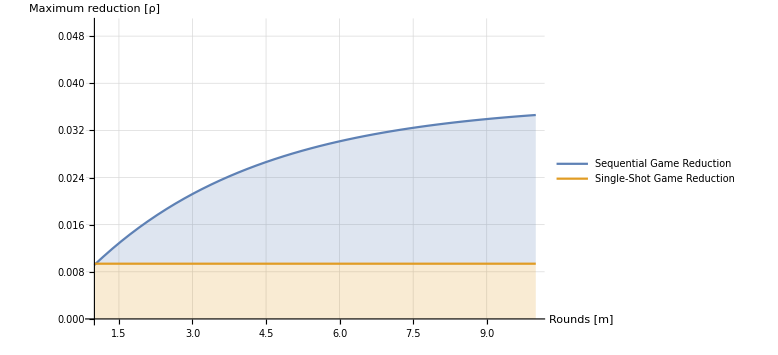

```mathematica
Plot[{rho2[mydelta,myr,x, x,myD, myp], linear}, {x,1,10}, AxesLabel->{"Rounds [m]", "Maximum reduction [ρ]"}, PlotLegends->{"Sequential Game Reduction", "Single-Shot Game Reduction"}, PlotRange->{{1,10},{0,0.05}}, AxesOrigin->{1,0},PlotTheme->"Default" , Filling->{{1-> {2}},{2 -> Bottom}}, GridLines->Automatic, ImageSize->Large]
```

```mathematica
rho2[mydelta,myr,0, 0, myD, myp]
rho2[mydelta,myr,10, 10, myD, myp]
linear
```

3.03826×10^-18

0.0346116

0.00937404